```mathematica
A2Lattice = Flatten[Table[If[a+b+c==0&&1/2(a^2+b^2+c^2)≤3,{a,b,c},Nothing],{a,-3,3},{b,-3,3},{c,-3,3}],2]
A2Roots= Table[If[1/2a.a==1,a,Nothing],{a,A2Lattice}];
σ={σ1,σ2,σ3};
Subscript[B, 0][{v1_,v2_,v3_}]:=Product[BarnesG[1+a.{v1,v2,v3}],{a,A2Roots}];
Subscript[B, 0][v1_,v2_,v3_]:=Subscript[B, 0][{v1,v2,v3}];
Subscript[Z, 1][{v1_,v2_,v3_}]:=(-Sum[1/Product[If[j≠i,-(Subscript[s, i]-Subscript[s, j])^2,1],{j,1,3}],{i,1,3}]/.{Subscript[s, 1]->v1,Subscript[s, 2]->v2,Subscript[s, 3]->v3});
Subscript[Z, 1][v1_,v2_,v3_]:=Subscript[Z, 1][{v1,v2,v3}];
```

{{-2,1,1},{-1,-1,2},{-1,0,1},{-1,1,0},{-1,2,-1},{0,-1,1},{0,0,0},{0,1,-1},{1,-2,1},{1,-1,0},{1,0,-1},{1,1,-2},{2,-1,-1}}

```mathematica
Tau[{σ1_,σ2_,σ3_},T_]:=Sum[T^(({σ1,σ2,σ3}+n).({σ1,σ2,σ3}+n)/2)Subscript[B, 0][{σ1,σ2,σ3}+n](1+T Subscript[Z, 1][{σ1,σ2,σ3}+n]),{n,A2Lattice}]
```

```mathematica
Plot3D[Tau[{x,y,-x-y},(π/21)^4],{x,-1,1},{y,-1,1},PlotPoints->10]
```

$Aborted

```mathematica
ycoord=0.5;
f[x_ ?NumericQ]:=Log[1+Log[1+Abs[Tau[ {1/2+I x,1/2+I ycoord,-1-I x-I ycoord},(π/21)^4]]]]
Attributes[f]={Listable};
```

```mathematica
times=Range[0.1,2,.01];
vals=f[times];
```

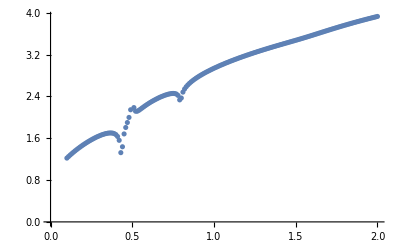

```mathematica
ListPlot[Transpose[{times,vals}]
]
```

```mathematica
{minD,maxD}={MinDetect@vals,MaxDetect@vals};

ListPlot[Transpose[{times,vals}],Epilog->{AbsolutePointSize[5],Green,Point@Pick[Transpose@{times,vals},maxD,1],Red,Point@Pick[Transpose@{times,vals},minD,1]}]
Log[1/(2π)Cosh[2π x/.x->Pick[Transpose@{times,vals},minD,1][[All,1]]]]
```

-Graphics-

```mathematica
DSolve[g'[t]==g[t]^2,g,t]
```

{{g→Function[{t},1/(-t-C[1])]}}

```mathematica
Show[ListPlot[Transpose[{times,vals}],Plot[ 1,Range[0.1,2,.01],Epilog->{AbsolutePointSize[5],Green,Point@Pick[Transpose@{times,vals},maxD,1],Red,Point@Pick[Transpose@{times,vals},minD,1]}]]]
```

Show[ListPlot[{{0.1,1.22046},{0.11,1.25006},{0.12,1.27855},{0.13,1.30602},{0.14,1.33252},{0.15,1.35813},{0.16,1.38288},{0.17,1.40681},{0.18,1.42996},{0.19,1.45234},{0.2,1.47398},{0.21,1.49489},{0.22,1.51507},{0.23,1.53452},{0.24,1.55323},{0.25,1.57118},{0.26,1.58836},{0.27,1.60473},{0.28,1.62024},{0.29,1.63483},{0.3,1.64843},{0.31,1.66094},{0.32,1.67223},{0.33,1.68212},{0.34,1.69037},{0.35,1.69667},{0.36,1.70054},{0.37,1.7013},{0.38,1.69787},{0.39,1.68843},{0.4,1.66959},{0.41,1.63398},{0.42,1.56036},{0.43,1.32456},{0.44,1.43732},{0.45,1.68277},{0.46,1.80595},{0.47,1.90105},{0.48,1.9984},{0.49,2.14521},{0.5,Indeterminate},{0.51,2.18678},{0.52,2.11765},{0.53,2.11657},{0.54,2.13352},{0.55,2.15547},{0.56,2.17854},{0.57,2.2014},{0.58,2.2236},{0.59,2.24496},{0.6,2.26545},{0.61,2.28506},{0.62,2.3038},{0.63,2.32171},{0.64,2.33877},{0.65,2.35502},{0.66,2.37043},{0.67,2.38498},{0.68,2.39864},{0.69,2.41135},{0.7,2.42301},{0.71,2.43349},{0.72,2.44258},{0.73,2.44998},{0.74,2.4552},{0.75,2.45745},{0.76,2.45525},{0.77,2.44549},{0.78,2.41971},{0.79,2.33391},{0.8,2.36998},{0.81,2.48279},{0.82,2.5418},{0.83,2.58488},{0.84,2.62013},{0.85,2.65067},{0.86,2.67804},{0.87,2.7031},{0.88,2.72639},{0.89,2.74827},{0.9,2.769},{0.91,2.78876},{0.92,2.80769},{0.93,2.82591},{0.94,2.84349},{0.95,2.8605},{0.96,2.87701},{0.97,2.89307},{0.98,2.9087},{0.99,2.92395},{1.,2.93885},{1.01,2.95342},{1.02,2.96768},{1.03,2.98166},{1.04,2.99537},{1.05,3.00882},{1.06,3.02204},{1.07,3.03504},{1.08,3.04782},{1.09,3.0604},{1.1,3.07278},{1.11,3.08498},{1.12,3.097},{1.13,3.10886},{1.14,3.12055},{1.15,3.13209},{1.16,3.14348},{1.17,3.15473},{1.18,3.16584},{1.19,3.17681},{1.2,3.18766},{1.21,3.19839},{1.22,3.20899},{1.23,3.21949},{1.24,3.22987},{1.25,3.24014},{1.26,3.25031},{1.27,3.26038},{1.28,3.27036},{1.29,3.28024},{1.3,3.29003},{1.31,3.29974},{1.32,3.30936},{1.33,3.31891},{1.34,3.32838},{1.35,3.33778},{1.36,3.34711},{1.37,3.35638},{1.38,3.36559},{1.39,3.37475},{1.4,3.38386},{1.41,3.39293},{1.42,3.40196},{1.43,3.41097},{1.44,3.41995},{1.45,3.42892},{1.46,3.4379},{1.47,3.44688},{1.48,3.45587},{1.49,3.4649},{1.5,3.47397},{1.51,3.48309},{1.52,3.49228},{1.53,3.50153},{1.54,3.51086},{1.55,3.52027},{1.56,3.52976},{1.57,3.53934},{1.58,3.54899},{1.59,3.55872},{1.6,3.56851},{1.61,3.57834},{1.62,3.58822},{1.63,3.59813},{1.64,3.60805},{1.65,3.61797},{1.66,3.62789},{1.67,3.63778},{1.68,3.64765},{1.69,3.65749},{1.7,3.66728},{1.71,3.67703},{1.72,3.68672},{1.73,3.69636},{1.74,3.70593},{1.75,3.71544},{1.76,3.72488},{1.77,3.73425},{1.78,3.74356},{1.79,3.75279},{1.8,3.76195},{1.81,3.77103},{1.82,3.78005},{1.83,3.78898},{1.84,3.79785},{1.85,3.80664},{1.86,3.81535},{1.87,3.82399},{1.88,3.83256},{1.89,3.84106},{1.9,3.84948},{1.91,3.85783},{1.92,3.86611},{1.93,3.87432},{1.94,3.88246},{1.95,3.89053},{1.96,3.89853},{1.97,3.90646},{1.98,3.91433},{1.99,3.92213},{2.,3.92986}},Plot[1,Range[0.1,2,0.01],Epilog→{AbsolutePointSize[5],Green,Point[Pick[Transpose[{times,vals}],maxD,1]],Red,Point[Pick[Transpose[{times,vals}],minD,1]]}]]]

```mathematica
Point@Pick[Transpose@{times,vals},maxD,1]
```

Point[Pick[{{0.1,1.22046},{0.11,1.25006},{0.12,1.27855},{0.13,1.30602},{0.14,1.33252},{0.15,1.35813},{0.16,1.38288},{0.17,1.40681},{0.18,1.42996},{0.19,1.45234},{0.2,1.47398},{0.21,1.49489},{0.22,1.51507},{0.23,1.53452},{0.24,1.55323},{0.25,1.57118},{0.26,1.58836},{0.27,1.60473},{0.28,1.62024},{0.29,1.63483},{0.3,1.64843},{0.31,1.66094},{0.32,1.67223},{0.33,1.68212},{0.34,1.69037},{0.35,1.69667},{0.36,1.70054},{0.37,1.7013},{0.38,1.69787},{0.39,1.68843},{0.4,1.66959},{0.41,1.63398},{0.42,1.56036},{0.43,1.32456},{0.44,1.43732},{0.45,1.68277},{0.46,1.80595},{0.47,1.90105},{0.48,1.9984},{0.49,2.14521},{0.5,Indeterminate},{0.51,2.18678},{0.52,2.11765},{0.53,2.11657},{0.54,2.13352},{0.55,2.15547},{0.56,2.17854},{0.57,2.2014},{0.58,2.2236},{0.59,2.24496},{0.6,2.26545},{0.61,2.28506},{0.62,2.3038},{0.63,2.32171},{0.64,2.33877},{0.65,2.35502},{0.66,2.37043},{0.67,2.38498},{0.68,2.39864},{0.69,2.41135},{0.7,2.42301},{0.71,2.43349},{0.72,2.44258},{0.73,2.44998},{0.74,2.4552},{0.75,2.45745},{0.76,2.45525},{0.77,2.44549},{0.78,2.41971},{0.79,2.33391},{0.8,2.36998},{0.81,2.48279},{0.82,2.5418},{0.83,2.58488},{0.84,2.62013},{0.85,2.65067},{0.86,2.67804},{0.87,2.7031},{0.88,2.72639},{0.89,2.74827},{0.9,2.769},{0.91,2.78876},{0.92,2.80769},{0.93,2.82591},{0.94,2.84349},{0.95,2.8605},{0.96,2.87701},{0.97,2.89307},{0.98,2.9087},{0.99,2.92395},{1.,2.93885},{1.01,2.95342},{1.02,2.96768},{1.03,2.98166},{1.04,2.99537},{1.05,3.00882},{1.06,3.02204},{1.07,3.03504},{1.08,3.04782},{1.09,3.0604},{1.1,3.07278},{1.11,3.08498},{1.12,3.097},{1.13,3.10886},{1.14,3.12055},{1.15,3.13209},{1.16,3.14348},{1.17,3.15473},{1.18,3.16584},{1.19,3.17681},{1.2,3.18766},{1.21,3.19839},{1.22,3.20899},{1.23,3.21949},{1.24,3.22987},{1.25,3.24014},{1.26,3.25031},{1.27,3.26038},{1.28,3.27036},{1.29,3.28024},{1.3,3.29003},{1.31,3.29974},{1.32,3.30936},{1.33,3.31891},{1.34,3.32838},{1.35,3.33778},{1.36,3.34711},{1.37,3.35638},{1.38,3.36559},{1.39,3.37475},{1.4,3.38386},{1.41,3.39293},{1.42,3.40196},{1.43,3.41097},{1.44,3.41995},{1.45,3.42892},{1.46,3.4379},{1.47,3.44688},{1.48,3.45587},{1.49,3.4649},{1.5,3.47397},{1.51,3.48309},{1.52,3.49228},{1.53,3.50153},{1.54,3.51086},{1.55,3.52027},{1.56,3.52976},{1.57,3.53934},{1.58,3.54899},{1.59,3.55872},{1.6,3.56851},{1.61,3.57834},{1.62,3.58822},{1.63,3.59813},{1.64,3.60805},{1.65,3.61797},{1.66,3.62789},{1.67,3.63778},{1.68,3.64765},{1.69,3.65749},{1.7,3.66728},{1.71,3.67703},{1.72,3.68672},{1.73,3.69636},{1.74,3.70593},{1.75,3.71544},{1.76,3.72488},{1.77,3.73425},{1.78,3.74356},{1.79,3.75279},{1.8,3.76195},{1.81,3.77103},{1.82,3.78005},{1.83,3.78898},{1.84,3.79785},{1.85,3.80664},{1.86,3.81535},{1.87,3.82399},{1.88,3.83256},{1.89,3.84106},{1.9,3.84948},{1.91,3.85783},{1.92,3.86611},{1.93,3.87432},{1.94,3.88246},{1.95,3.89053},{1.96,3.89853},{1.97,3.90646},{1.98,3.91433},{1.99,3.92213},{2.,3.92986}},MaxDetect[{1.22046,1.25006,1.27855,1.30602,1.33252,1.35813,1.38288,1.40681,1.42996,1.45234,1.47398,1.49489,1.51507,1.53452,1.55323,1.57118,1.58836,1.60473,1.62024,1.63483,1.64843,1.66094,1.67223,1.68212,1.69037,1.69667,1.70054,1.7013,1.69787,1.68843,1.66959,1.63398,1.56036,1.32456,1.43732,1.68277,1.80595,1.90105,1.9984,2.14521,Indeterminate,2.18678,2.11765,2.11657,2.13352,2.15547,2.17854,2.2014,2.2236,2.24496,2.26545,2.28506,2.3038,2.32171,2.33877,2.35502,2.37043,2.38498,2.39864,2.41135,2.42301,2.43349,2.44258,2.44998,2.4552,2.45745,2.45525,2.44549,2.41971,2.33391,2.36998,2.48279,2.5418,2.58488,2.62013,2.65067,2.67804,2.7031,2.72639,2.74827,2.769,2.78876,2.80769,2.82591,2.84349,2.8605,2.87701,2.89307,2.9087,2.92395,2.93885,2.95342,2.96768,2.98166,2.99537,3.00882,3.02204,3.03504,3.04782,3.0604,3.07278,3.08498,3.097,3.10886,3.12055,3.13209,3.14348,3.15473,3.16584,3.17681,3.18766,3.19839,3.20899,3.21949,3.22987,3.24014,3.25031,3.26038,3.27036,3.28024,3.29003,3.29974,3.30936,3.31891,3.32838,3.33778,3.34711,3.35638,3.36559,3.37475,3.38386,3.39293,3.40196,3.41097,3.41995,3.42892,3.4379,3.44688,3.45587,3.4649,3.47397,3.48309,3.49228,3.50153,3.51086,3.52027,3.52976,3.53934,3.54899,3.55872,3.56851,3.57834,3.58822,3.59813,3.60805,3.61797,3.62789,3.63778,3.64765,3.65749,3.66728,3.67703,3.68672,3.69636,3.70593,3.71544,3.72488,3.73425,3.74356,3.75279,3.76195,3.77103,3.78005,3.78898,3.79785,3.80664,3.81535,3.82399,3.83256,3.84106,3.84948,3.85783,3.86611,3.87432,3.88246,3.89053,3.89853,3.90646,3.91433,3.92213,3.92986}],1]]

```mathematica
Tau[{x,y,-x-y},(π/21)^4]/.{x->0.3,y->-0.1}//N
```

0.134991

```mathematica
-Sum[1/Product[If[j≠i,-(Subscript[s, i]-Subscript[s, j])^2,1],{j,1,3}],{i,1,3}]
```

-(2 (s_1^2+s_2^2-s_2 s_3+s_3^2-s_1 (s_2+s_3)))/((s_1-s_2)^2 (s_1-s_3)^2 (s_2-s_3)^2)